## Lahka varianta

Sestavite funkcijo vogali[n_], ki vrne sliko vogalov, kot je prikazano na sliki za n=7

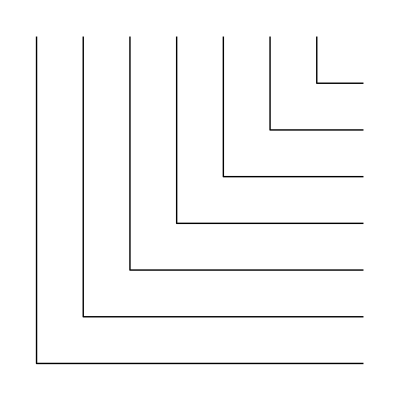

### Rešitev:

```mathematica
vogali[n_]:=Graphics[Table[Line[{{-k,0},{-k,-k},{0,-k}}],{k,1,n}]]
```

## Težja varianta

Sestavite funkcijo kaca[n_], ki vrne sliko, kot je prikazano na sliki za n=7

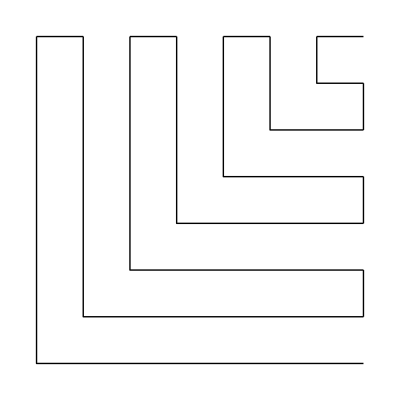

```mathematica
Export["kaca6.pdf",kaca[6]]
```

kaca6.pdf

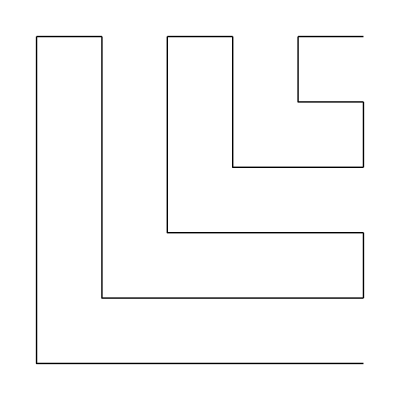

```mathematica
kaca[5]
```

### Rešitev:

```mathematica
kaca[n_]:=Graphics[{
Table[Line[{{-k,0},{-k+1,0}}],{k,1,n,2}],
Table[Line[{{0,-k},{0,-k+1}}],{k,2,n,2}],
Table[Line[{{-k,0},{-k,-k},{0,-k}}],{k,1,n}]}]
```